# Gossip Algorithms over different network topologies

A brief description of three different gossip algorithms, Probabilistic Broadcast, Probabilistic Edge, Fixed Fanout, with detailed example on how do they work over different network topologies, Erdős–Rényi, Random Geometric Graph, scale free.

## Random Graph

Gossip algorithms are a system of machine-to-machine communication whose goal is to minimize the channel usage and maximise the coverage of the network. Network can be seen as graph of nodes, nodes represent computers and edges represent connections.

Example of a random graph:

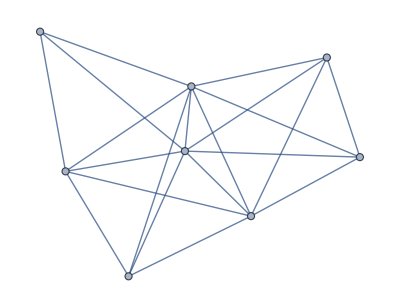

```mathematica
randomGraph=RandomGraph[{8,20}]
```

A pure mechanism of broadcast send the message to all the other node connected with the source, this method leads to a complete coverage of the message in the graph but on the other hand cause the saturation of the channel.

In red the source of the message, mails on involved edges

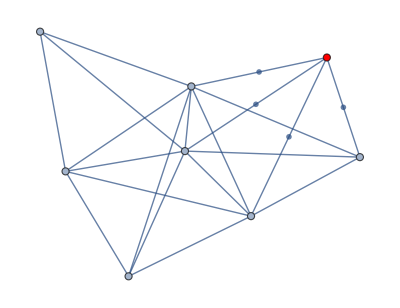

```mathematica
SetProperty[{SetProperty[{randomGraph, EdgeList[randomGraph,1<->_ ]}, EdgeLabels -> -Graphics-],1},VertexStyle->Red]
```

## Symbols and Functions

There are three famous gossip algorithm, their difference is mostly related on how do they choose the node to whom forward the messages. They are named in literature: Probabilistic Broadcast (PB), Probabilistic Edge (PE) e Fixed Fanout (FF).
In order to better understand the algorithms it’s important to introduce some notation

Λ = set of node adjacent to node i.

1→{2,4,5,8}

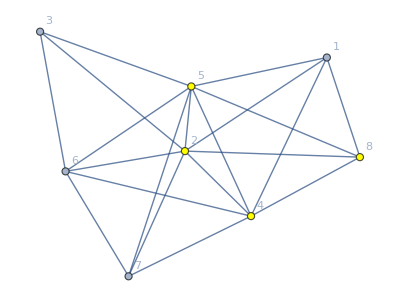

```mathematica
Λ[graph_,i_]:=Map[Last,EdgeList[graph,i<->_ ]]
1->Λ[randomGraph,1]
SetProperty[{SetProperty[randomGraph,VertexLabels->"Name"],Λ[randomGraph,1]},VertexStyle->Yellow]
```

V = cardinality of Λ_i

```mathematica
V[graph_,i_]:=Length[Λ[graph,i]]
V[randomGraph,1]
```

4

msg = the message received
p_v , p_e , fanout = probabilistic value related with the algorithm, PB,PE,EF.

## Probabilistic Broadcast

The first algorithm is Probabilistic Broadcast, the value p_v is the threshold that decide if the message will be send in broadcast or dropped from the node i .

example of Probabilistic Broadcast with p_v= 0.3

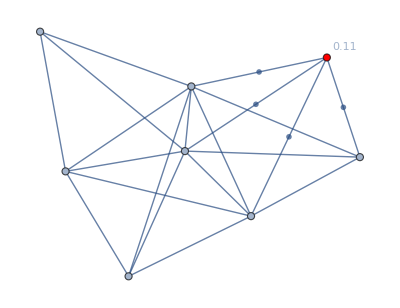
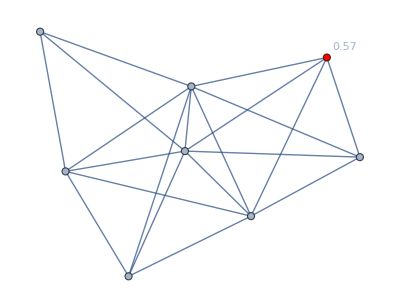
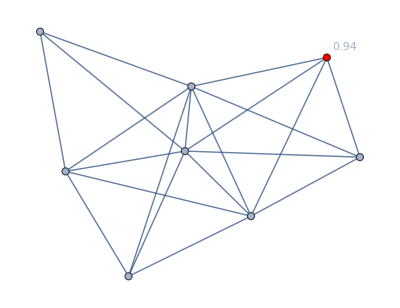
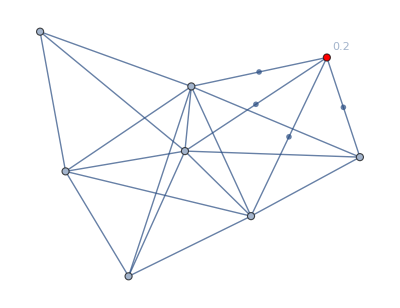
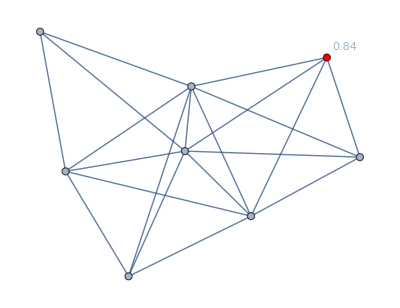
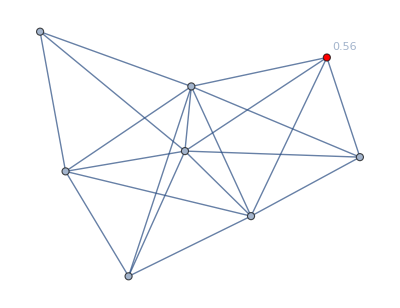
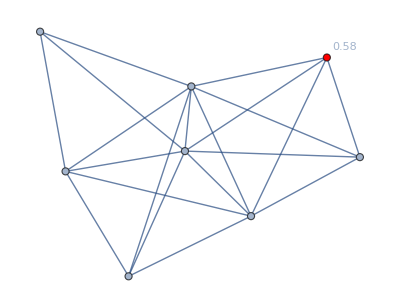
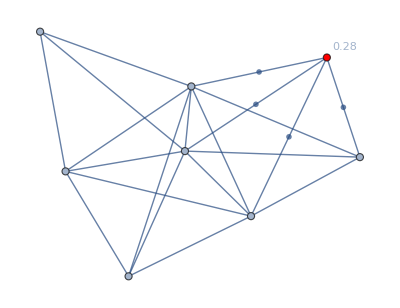

```mathematica
ProbabilisticBroadcast[graph_,i_,msg_,pv_]:= With[
{r=RandomReal[]},If[
r≤ pv,
SetProperty[{SetProperty[{SetProperty[{graph, EdgeList[graph,i<->_ ]}, EdgeLabels -> msg],i},VertexStyle->Red],i},VertexLabels->{SetPrecision[r,2]}],
SetProperty[{SetProperty[{graph,i},VertexStyle->Red],i},VertexLabels->{SetPrecision[r,2]}]
]]
Table[ProbabilisticBroadcast[randomGraph,1,-Graphics-,.3],{x,1,10}]
```

## Probabilistic Edge

The second algorithm is Probabilistic Edge, the value p_e  is the threshold that decide if the message will be send on a specific arc or not, from the node i.

example of edge selection with Probabilistic Edge with p_e= 0.3

```mathematica
GetEdge[graph_,i_,pe_]:=Map[First,Select[Map[With[{r=RandomReal[]≤pe},{#,r}]&,Map[i->#&,Λ[graph,1]]],Last[#]==True&]]
GetEdge[randomGraph,1,.3]
```

{1→4,1→5}

example Probabilistic Edge with p_e= 0.4

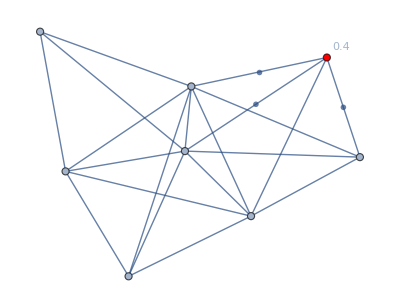
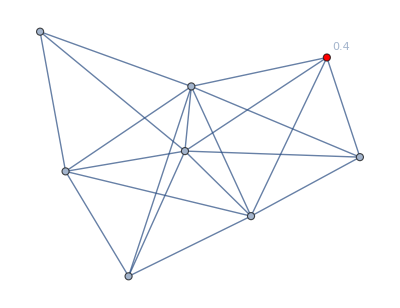
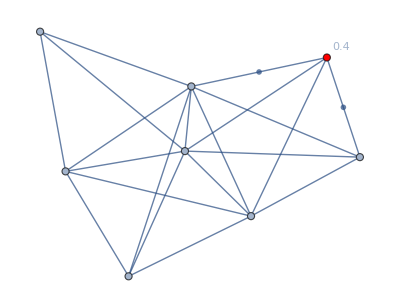
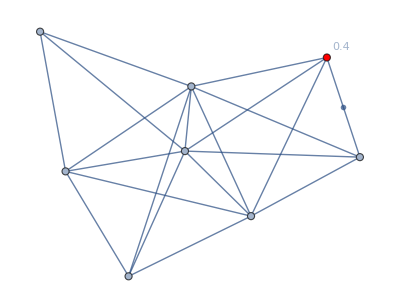
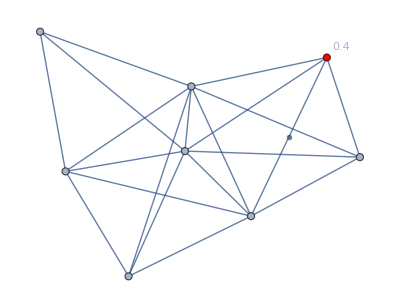
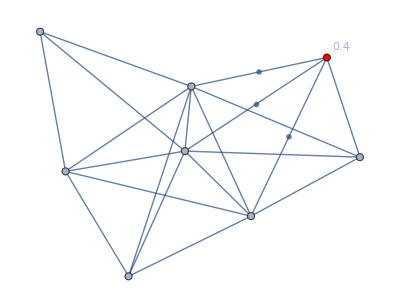
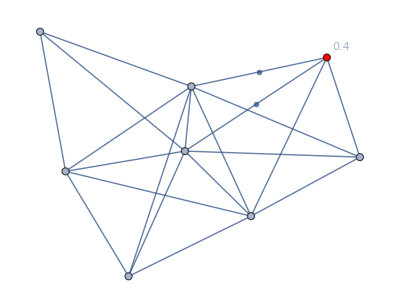
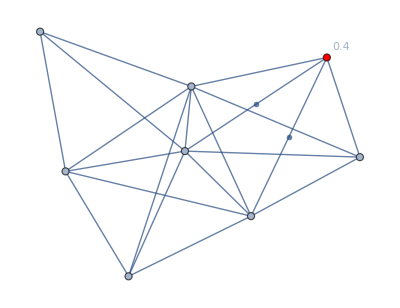
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[ProbabilisticEdge]
ProbabilisticEdge[graph_,i_,msg_,pe_]:=
SetProperty[{SetProperty[{SetProperty[{graph, GetEdge[graph,i,pe ]}, EdgeLabels -> msg],i},VertexStyle->Red],i},VertexLabels->{SetPrecision[pe,2]}]
Table[ProbabilisticEdge[randomGraph,1,-Graphics-,.4],{x,1,10}]
```

It’s expected a number of message  ~ V_1 * n°Example * p_e

```mathematica
V[randomGraph,1]*10*.4
```

16.

## Fixed Fanout

The last algorithm is Fixed Fanout the node choose a number of random node connected with him to whom send the message.

example of fanout selection with Fixed Fanout with 0<= fanout <= V_i

```mathematica
Clear[GetEdgeFanout]
GetEdgeFanout[graph_,i_,fanout_]:=RandomSample[Map[i->#&,Λ[graph,1]],fanout]
GetEdgeFanout[randomGraph,1,RandomInteger[{0,V[randomGraph,1]}]]
```

{1→8,1→2,1→4}

example Fixed Fanout with  0<= fanout <= V_i

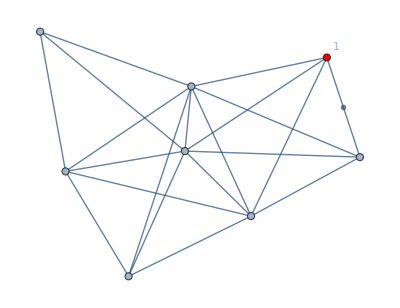
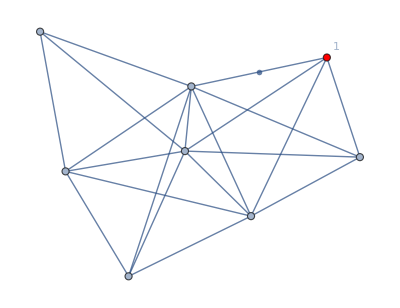
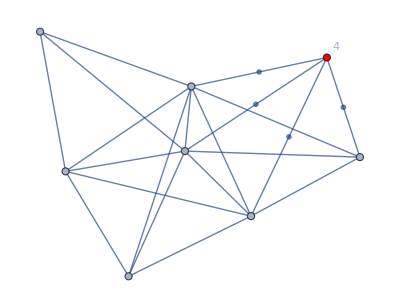
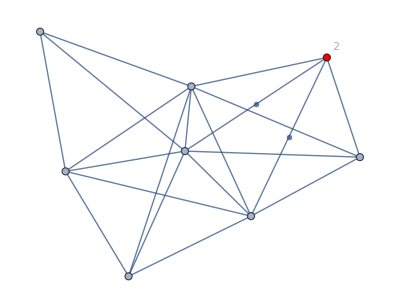
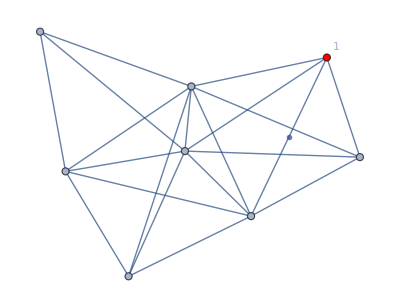
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[FixedFanout]
FixedFanout[graph_,i_,msg_,fanout_]:=SetProperty[{SetProperty[{SetProperty[{graph, GetEdgeFanout[graph,i,fanout]}, EdgeLabels -> msg],i},VertexStyle->Red],i},VertexLabels->{fanout}]
Table[FixedFanout[randomGraph,1,-Graphics-,RandomInteger[{0,V[randomGraph,1]}]],{x,1,10}]
```

## Erdős–Rényi or Bernulli graph

There are an infinity number of graph topologies here are shown only the ones more important for this case study.
Erdős–Rényi graph also called Bernulli graph is one of the most important way to generate random graphs.
A Bernoulli graph distribution leads to graph with n-vertex and edge probability p.

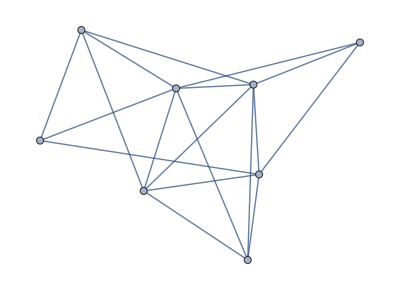

```mathematica
RandomGraph[BernoulliGraphDistribution[8,.6]]
```

The variance of vertex degree represent the variance of number of edge that each node are linked with. 
It’s an important parameter that can impact in the spreading of the message a low variance in vertex degree can cause the dropping of a message before the coverage is complete.

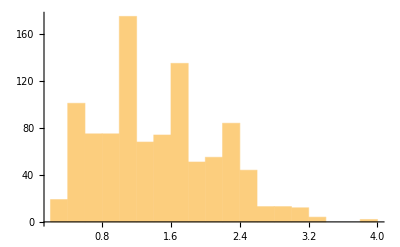

```mathematica
vVertexDegree=Variance /@VertexDegree /@ RandomGraph[BernoulliGraphDistribution[8,0.6],10^3];
Show[Histogram[vVertexDegree,Automatic]]
```

The edge connectivity represent the minimum number of edge that should be deleted from a graph to make it disconnected.

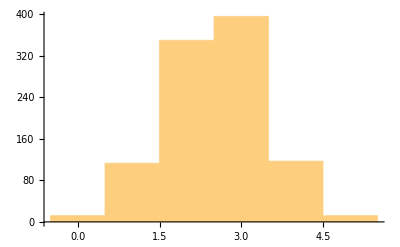

```mathematica
edgeConnectivity=EdgeConnectivity /@ RandomGraph[BernoulliGraphDistribution[8,0.6],10^3];
Show[Histogram[edgeConnectivity,Automatic]]
```

## Random Geometric Graph

Random Geometric graph also called spatial graph is network really common in everyday life they can represent the connection of streets or railroads between cities and they are really useful in literature.
A Random Geometric graph is made by spreading node randomly in a plane then adding edge on each node if the distance between the node is less then p_(e.)

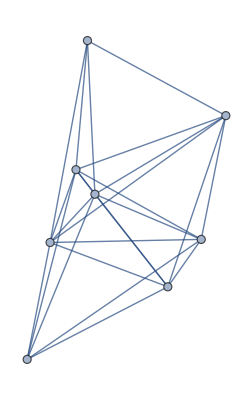

```mathematica
RandomGraph[SpatialGraphDistribution[8,.6]]
```

Variance of the vertex degree of a Random Geometric graph

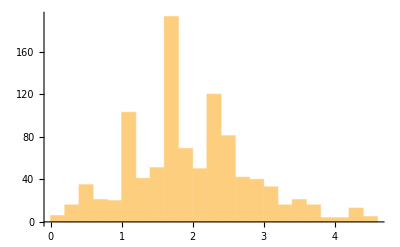

```mathematica
vVertexDegreeSG=Variance /@VertexDegree /@ RandomGraph[SpatialGraphDistribution[8,0.6],10^3];
Show[Histogram[vVertexDegreeSG,Automatic]]
```

Edge connectivity of a Random Geometric graph

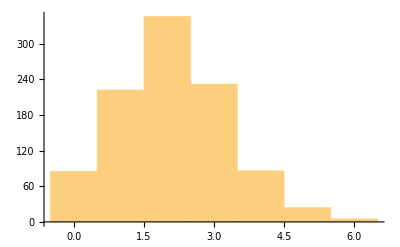

```mathematica
edgeConnectivitySG=EdgeConnectivity /@ RandomGraph[SpatialGraphDistribution[8,0.6],10^3];
Show[Histogram[edgeConnectivitySG,Automatic]]
```

## Example of Random Geometric graph

A typical example of Random Geometric graph are rails or highways, they share the same structure due two the fact that nears cities are commonly connected with a path.

An example of highways graph of Italy city:

```mathematica
Clear[rawHighways]
Clear[highways]
rawHighways=Import[FileNameJoin[{NotebookDirectory[],"assets/highways.csv"}]];
highways=Values[GroupBy[rawHighways,Last,ToLowerCase[StringSplit[#[[All,2]]][[All,1]]]&]];
highwaysGraph=Graph[Flatten[Map[Function[l, Table[l[[i]]<->l[[i+1]],{i,1,Length[l]-1}]],highways]]]
```

-Graphics-

The vertex degree is strictly related with political or economical influence and also with centrality in the map:

```mathematica
Select[#->VertexDegree[highwaysGraph,#]&/@VertexList[highwaysGraph],Last[#]==Max[VertexDegree[highwaysGraph]]&]
```

{firenze→9}

An example of map of Italy highways with names of most connected city:

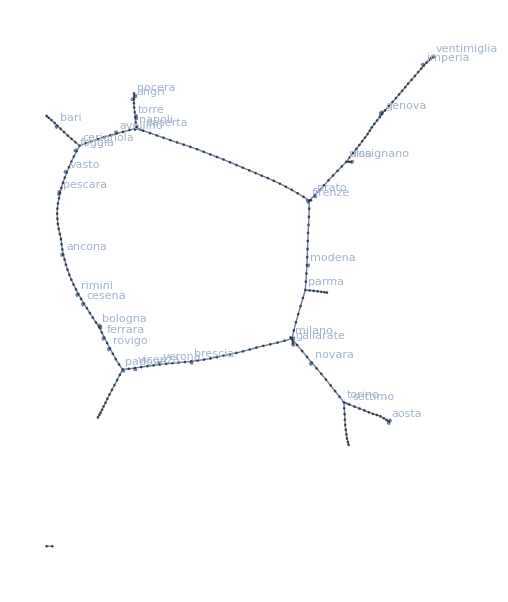

```mathematica
importantCity=Map[First[#]->First[#]&,Select[#->VertexDegree[highwaysGraph,#]&/@VertexList[highwaysGraph],Last[#]>Mean[VertexDegree[highwaysGraph]]&]];
Graph[Flatten[Map[Function[l, Table[l[[i]]<->l[[i+1]],{i,1,Length[l]-1}]],highways]],VertexLabels->importantCity]
```

## Scale Free graph

Scale Free graph also known as small world graph is network whose popularity is growing really fast in those year they are common in study of Social Network connection between people, they can also model airline flight between city, or link between web page.
A Scale Free graph can be made with the Barabasi Albert distribution, generating a clique of m_0 node and then connecting each node m to node where m ≤ m_0 with a probability related with the V of each node.

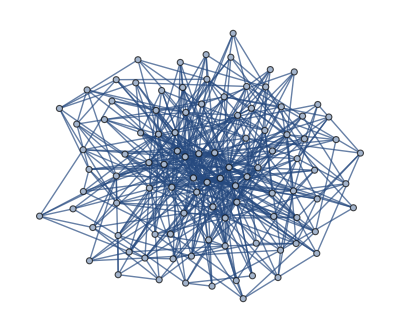

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[100,5]]
```

Variance of the vertex degree of a Scale Free graph:

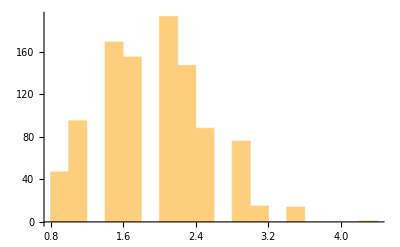

```mathematica
vVertexDegreeSF=Variance /@VertexDegree /@ RandomGraph[BarabasiAlbertGraphDistribution[8,3],10^3];
Show[Histogram[vVertexDegreeSF,Automatic]]
```

Edge connectivity of a Scale Free graph:

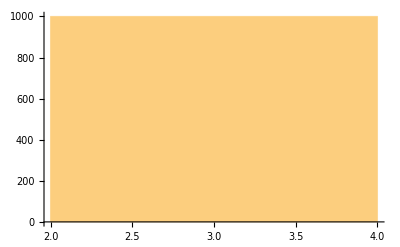

```mathematica
edgeConnectivitySF=EdgeConnectivity /@ RandomGraph[BarabasiAlbertGraphDistribution[8,3],10^3];
Show[Histogram[edgeConnectivitySF,Automatic]]
```

## Example of Scale Free graph

Internet is an example of Scale Free graph, here the info.cern.ch hyperlinks network:

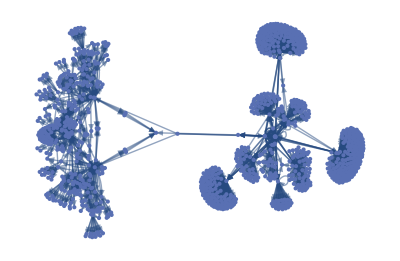

```mathematica
NestGraph[Import[#,"Hyperlinks"]&,"http://info.cern.ch",3,VertexLabels->Placed["Name",Tooltip]]
```

## Comparison between the graph topology

It’s important to check the comparison between different aspect of each graph.

Comparison of variance of the vertex degree between Erdős–Rényi, Random Geometric, and Scale Free graph:

```mathematica
{Show[Histogram[vVertexDegree,Automatic]],Show[Histogram[vVertexDegreeSG,Automatic]],Show[Histogram[vVertexDegreeSF,Automatic]]}
```

{-Graphics-,-Graphics-,-Graphics-}

Comparison of edge connectivity between Erdős–Rényi, Random Geometric, and Scale Free graph

```mathematica
{Show[Histogram[edgeConnectivity,Automatic]],Show[Histogram[edgeConnectivitySG,Automatic]],Show[Histogram[edgeConnectivitySF,Automatic]]}
```

{-Graphics-,-Graphics-,-Graphics-}

It can be seen in the previous graphs that each network has different behaviour over those important aspects.
Studying the mean of variation of vertex degree it can be understand better which graph has a more peculiar topology with high isolated nodes and cluster.

Random Geometric graph due to its unique topology shuld have the higher Variation of Vertex Degree, followed by Scale Free due to the presence of hub’s nodes, Erdős–Rényi on the other hand has a very low Vertex Degree variation.

```mathematica
w={"Erdős–Rényi"->N[Mean[vVertexDegree]],"Random Geometric"->N[Mean[vVertexDegreeSG]],"Scale Free"->N[Mean[vVertexDegreeSF]]}
max = Max[Map[Last,w]];
Select[w,Last[#]==max&]
```

{Erdős–Rényi→1.439,Random Geometric→1.96029,Scale Free→1.92086}

{Random Geometric→1.96029}

It can also be compared the edge connectivity in order to properly understand the fault tolerance of those network and the reliability of the infrastructure.

Scale Free graph do the presence of macro hub and clique has the higher edge connectivity, followed by  Erdős–Rényi ,  and Random Geometric due to the isolated nodes.

```mathematica
w={"Erdős–Rényi"->N[Mean[edgeConnectivity]],"Random Geometric"->N[Mean[edgeConnectivitySG]],"Scale Free"->N[Mean[edgeConnectivitySF]]}
max = Max[Map[Last,w]];
Select[w,Last[#]==max&]
```

{Erdős–Rényi→2.529,Random Geometric→2.104,Scale Free→3.}

{Scale Free→3.}

## Conclusion

Gossip Algorithms could be really useful in situation of network instability where the network topology change really fast, they can also be used to simulate human spreading of information and virus diffusion over population.

Further Explorations

Graph Theory

Social Network

Torrent and Peer To Peer

Routing

Authorship information

Daniele Baschieri

20/06/2017

daniele.baschieri@gmail.com